### Plot Style

```mathematica
MyFont="Times";
MyLabelSize=18;
MyTickSize=18;
```

```mathematica
MyOptions=Sequence[LabelStyle->Black, TicksStyle->Black,
Axes->None,
Frame->True(*,
AspectRatio->1*),LabelStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameTicksStyle->Directive[Black,FontFamily->MyFont,FontSize->MyTickSize],
ImageSize->{360,359},
Axes->None];

LogTiks[x_,y_]:=Flatten[Table[{{2*10^i,""},{3*10^i,""},{4*10^i,""},{5*10^i,""},{6*10^i,""},{7*10^i,""},{8*10^i,""},{9*10^i,""},{10*10^i,10*10^i}},{i,x,y}],1]//N;
```

```mathematica
LogTiks2[x_,y_]:=Flatten[Table[{{2*10^i,""},{3*10^i,""},{4*10^i,""},{5*10^i,""},{6*10^i,""},{7*10^i,""},{8*10^i,""},{9*10^i,""},{10^i,Which[i==0,"1",i==1,"10",i=!=0&&i=!=1,"10"^ToString[i]]}},{i,x,y}],1]//N;
```

```mathematica
Options[burnTooltips]={ImageSize->360,"LabelFunction"->(Framed[#,FrameStyle->None,RoundingRadius->7,Background->RGBColor[0.94,0.94,0.94,0.94]]&)};
RGBColor[0.98,0.98,0.98,0.98]
```

RGBColor[0.98, 0.98, 0.98, 0.98]

```mathematica
LogTiks3[x_,y_]:=Flatten[Table[{{Log[10,2*10^i],""},{Log[10,3*10^i],""},{Log[10,4*10^i],""},{Log[10,5*10^i],""},{Log[10,6*10^i],""},{Log[10,7*10^i],""},{Log[10,8*10^i],""},{Log[10,9*10^i],""},{Log[10,10*10^i],Which[i==0,"10",i==-1,"1",i=!=0&&i=!=-1,"10"^ToString[i+1]]}},{i,x,y}],1]//N;

LogTiks32[x_,y_]:=Flatten[Table[{{Log[10,2*10^i],""},{Log[10,3*10^i],""},{Log[10,4*10^i],""},{Log[10,5*10^i],""},{Log[10,6*10^i],""},{Log[10,7*10^i],""},{Log[10,8*10^i],""},{Log[10,9*10^i],""},{Log[10,10*10^i],Which[i+1==0,"1",i=!=0&&IntegerQ[(i+1)/2],"10"^ToString[i+1]]}},{i,x,y}],1]//N;





LogTiks32N[x_,y_]:=Flatten[Table[{{Log[10,2*10^i],""},{Log[10,3*10^i],""},{Log[10,4*10^i],""},{Log[10,5*10^i],""},{Log[10,6*10^i],""},{Log[10,7*10^i],""},{Log[10,8*10^i],""},{Log[10,9*10^i],""},{Log[10,10*10^i],""}},{i,x,y}],1]//N;

burnTooltips[plot_,opt:OptionsPattern[]]:=DynamicModule[{ins={},wrapper=OptionValue["LabelFunction"],toolRule=Function[{arg},Tooltip[t__]:>Button[Tooltip[t],AppendTo[arg,Inset[wrapper[Last[{t}]],MousePosition["Graphics"]]]],HoldAll]},EventHandler[Dynamic@Show[plot/.toolRule[ins],Graphics@ins,ImageSize->OptionValue[ImageSize]],{"MouseUp",2}:>(toolRule={}&)]]
SetDirectory["~/Downloads/MathematicaConfig/mmapkg"]
<<FixPolygons`
```

/Users/Sonia/Downloads/MathematicaConfig/mmapkg

```mathematica
ResourceFunction["MaTeXInstall"][];
(*SetDirectory["/Users/martinbauer/work/Mathematica Packages"];*)
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"];
{"CacheSize"->100,"pdfLaTeX"->"/usr/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{color,txfonts}"}];
MaTeX["\\color{red}\\sqrt{x}"];
{"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{color,txfonts}"},"DisplayStyle"->True,FontSize->12,Magnification->1};
```

### Preparations and inputs

#### SM input parameters

```mathematica
Off[General::spell,General::spell1]
```

Factor hbar*c in units GeV*m:

```mathematica
hbarc=1.973269788 10^-16;
```

Electroweak gauge-boson masses and Z-boson width:

```mathematica
mZ=91.1876;
mW=80.385;
ΓZ=2.4952;
```

Higgs mass and total width in the SM:

```mathematica
mh=125.09;
Gammah=4.08 10^-3;
```

Electroweak mixing angle from the Z-boson couplings at μ=m_Z:

```mathematica
s2W=0.23126;
c2W=1-s2W;
```

Lepton masses:

```mathematica
me=0.0005109989461;
mmu=0.1056583745;
mtau=1.77686;
```

QED coupling on-shell and at μ=m_Z:

```mathematica
alphaQED=1/137.036;
alphamZ=1/127.940;
```

Higgs vacuum expectation value:

```mathematica
v=√((s2W(1-s2W)mZ^2)/(π alphamZ))
```

245.36

Running heavy-quark masses m_q(m_q):

```mathematica
mt=163.40;
mb=4.180;
mc=1.275;
md=4.8*10^-3(*wiki*);
mu=2.3*10^-3(*wiki*);
ms=.95(*wiki*);
```

Top-quark properties:

```mathematica
mtpole=172.44;
```

```mathematica
Qt=2/3;
T3t=1/2;
vt=T3t/2-2/3 s2W;
```

```mathematica
yt=(√2 mt)/v;
```

Number of colors and strong coupling α_s(m_Z):

```mathematica
Nc=3;
```

```mathematica
alphasmZ=0.1185;
```

CKM matrix elements:

```mathematica
Vud=0.97425+ϵ 0.00022σckm;
Vus=0.2253+ϵ 0.0008σckm;
Vcd=0.225+ϵ 0.008σckm;
Vcs=0.986+ϵ 0.016σckm;
Vub=0.00413+ϵ 0.00049σckm;
Vcb=0.0411+ϵ 0.0013σckm;
Vtb=0.999;
Vts=40.0(*±2.7*)*10^-3;
Vtd=8.4(*±0.6*)*10^-3;
```

Phase-space function:

```mathematica
lambda[x_,y_,z_]:=(x-y-z)^2-4y z
```

New physics scale in units of GeV:

```mathematica
Lambda=1000;
```

Confidence Levels

```mathematica
CL68=Sqrt[2]*InverseErf[{.68,.95,.99}][[1]];
CL95=Sqrt[2]*InverseErf[{.68,.95,.99}][[2]]
CL99=Sqrt[2]*InverseErf[{.68,.95,.99}][[3]];
```

1.95996

```mathematica
colors=DominantColors[-Graphics-,6,MinColorDistance->.2]
```

{RGBColor[1., 0.9999994542917262, 0.9999990613752895],RGBColor[0.9617731484600017, 0.922549411185509, 0.6009786353209211],RGBColor[0.7823582653145473, 0.5156918224937027, 0.947058543399827],RGBColor[0.4444955204403427, 0.7176421764302292, 0.9320267489198844],RGBColor[0.917647637590094, 0.7137245922763765, 0.6392149582340969],RGBColor[0.8705886846707637, 0.6509795236120627, 0.7607835002674332]}

### Input

```mathematica
Get["~/Downloads/MathematicaConfig/RunDec.m"]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
(*Three-loop runnin(*g coupling Subscript[α, s] from the RunDec program by M.Steinhauser*)
Set some variables needed by the program:*)
NumDef={asMz->alphasmZ,Mz->mZ,Mt->mt,Mb->mb,Mc->mc};
(*Define the 3-loop running coupling:*)
LoopOrder=3;
as[μ_]:=AsRunDec[alphasmZ,mZ,μ,LoopOrder]
asmZ=as[mZ];
asmW=as[mW];
asmh=as[mh];
asmt=as[mt];
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

### Data

```mathematica
SetDirectory["~/Downloads/Electron_Coupling"];
```

```mathematica
XMASS={First[#]*10^-6,Lambda/me* Last[#]}&/@
Cases[Import["XMASS.txt","Table"],{_?NumericQ,__}];
edelweiss={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Edelweiss_Solid.txt","Table"],{_?NumericQ,__}];
edelweiss2={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Edelweiss_Dashed.txt","Table"],{_?NumericQ,__}];
```

```mathematica
edelweiss={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Edelweiss_Solid.txt","Table"],{_?NumericQ,__}];
edelweiss2={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Edelweiss_Dashed.txt","Table"],{_?NumericQ,__}];
Derbin={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Derbin_Solid.txt","Table"],{_?NumericQ,__}];
Derbin2={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Derbin_Dashed.txt","Table"],{_?NumericQ,__}];
Borexino={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Borexino_Dashed.txt","Table"],{_?NumericQ,__}];
SolarNeurtinos={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Solar_neutrinos.txt","Table"],{_?NumericQ,__}];
CuoreRD={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["CuoreRD_Dashed.txt","Table"],{_?NumericQ,__}];
RedGiant={First[#]*10^-6,Lambda/me* Last[#]}&/@Cases[Import["Red_Giant.txt","Table"],{_?NumericQ,__}];
CMSCah0p01={First[#], Last[#]}&/@
Cases[Import["CMSRun2ALP_cll_TeV_Cah_0p01.txt","Table"],{_?NumericQ,__}];
CMSCah0p1={First[#], Last[#]}&/@
Cases[Import["CMSRun2ALP_cll_TeV_Cah_0p1.txt","Table"],{_?NumericQ,__}];
CMSCah1={First[#], Last[#]}&/@
Cases[Import["CMSRun2ALP_cll_TeV_Cah_1.txt","Table"],{_?NumericQ,__}];
Beamdumpa={First[#],Lambda*1/ Last[#]}&/@Cases[Import["1008.0636_Fig5.txt","Table"],{_?NumericQ,__}];
Beamdump=Join[Beamdumpa,{Beamdumpa[[1]]}];
Babarplot=Join[ {{0.211316749,12.153345048898236}},ReadList["bbdata.dat"]];
```

```mathematica
EWlifetime1={10^First[#],10^ Last[#]}&/@Drop[EWlifetime1kev,-372];
```

```mathematica
EWlifetime1kev=({{-4.680470771354014, 4.}, {-4.674232111998949, 3.9713789139761513}, {-4.670214154048486, 3.9599408795295514}, {-4.665402789100535, 3.9364245694952955}, {-4.656577958441699, 3.905172413793104}, {-4.654393858361328, 3.8940715594794466}, {-4.648329310274392, 3.867329136354994}, {-4.646583653231281, 3.8609539592770323}, {-4.645626883338979, 3.8577586206896557}, {-4.644105916112459, 3.8500279072665453}, {-4.638277821247832, 3.8287435794337763}, {-4.6327687425250845, 3.8103448275862077}, {-4.630030370430847, 3.796426335762534}, {-4.622440403700708, 3.7629564688668697}, {-4.622432787965386, 3.76293103448276}, {-4.622431125328827, 3.7629225836979296}, {-4.622426508549836, 3.762902224850018}, {-4.61378363680954, 3.731337589188464}, {-4.609046678681255, 3.7155172413793114}, {-4.6057310004714, 3.6986637472815658}, {-4.600417123978018, 3.6752301551590953}, {-4.5985203186994354, 3.6681034482758634}, {-4.597817366655792, 3.6657354681553183}, {-4.596523706825279, 3.659564945022093}, {-4.5924866223680265, 3.6443965517241397}, {-4.589348163322779, 3.633824131459967}, {-4.585415486289588, 3.6206896551724155}, {-4.581498492801113, 3.6007787706984002}, {-4.578555378084369, 3.5877995211090967}, {-4.574206757013033, 3.573275862068967}, {-4.57325737166634, 3.5684499408579837}, {-4.570620905100721, 3.556823021460537}, {-4.564973919696007, 3.5361985955113524}, {-4.5618790587981115, 3.5258620689655187}, {-4.557335721670393, 3.5027661448403045}, {-4.5568620555173815, 3.5006771776003713}, {-4.550946067129523, 3.4784482758620703}, {-4.548753452939134, 3.4710617687454537}, {-4.545332103252664, 3.454741379310346}, {-4.544718103376164, 3.452115422711861}, {-4.5406635450659145, 3.4384561505338804}, {-4.538441474405453, 3.4310344827586223}, {-4.534909987340084, 3.413081213092492}, {-4.532811216128738, 3.4054156558699806}, {-4.526285734735847, 3.3836206896551744}, {-4.524308034379318, 3.3735665149796485}, {-4.518815301651607, 3.34934134858199}, {-4.5164198065496866, 3.340591731456866}, {-4.5151070077831115, 3.336206896551726}, {-4.5130207868020165, 3.3256003246783488}, {-4.508242245066398, 3.308146558828622}, {-4.50244791234876, 3.2887931034482776}, {-4.49992365853732, 3.2759595255481835}, {-4.4929124999270496, 3.2450359622358462}, {-4.49224560780271, 3.2426000232832206}, {-4.491989731852491, 3.241379310344829}, {-4.491299424919014, 3.238426656593138}, {-4.483729198666975, 3.210775094467114}, {-4.47869664040198, 3.193965517241381}, {-4.47560299469884, 3.1782359144560517}, {-4.469420042891957, 3.1509637404761466}, {-4.468099145347063, 3.1465517241379324}, {-4.467810758237752, 3.1450854234968237}, {-4.467009698202492, 3.141552054754466}, {-4.459274531626424, 3.1132967695863267}, {-4.455035710184384, 3.099137931034484}, {-4.451348847865182, 3.08039054728757}, {-4.447505295883944, 3.0634360905165394}, {-4.44399901423762, 3.051724137931036}, {-4.443233490323265, 3.0478315134315808}, {-4.441106896477935, 3.0384508042344147}, {-4.434880824896961, 3.015706859881313}, {-4.432492273158937, 3.004310344827588}, {-4.428155495615656, 2.985758343448719}, {-4.4271641687540955, 2.982418022900329}, {-4.425758068974237, 2.9762150777835252}, {-4.419974777116081, 2.9568965517241397}, {-4.418712098026728, 2.9504753258205665}, {-4.415204094753378, 2.934999929205147}, {-4.410550795192389, 2.918000392542273}, {-4.408001021451503, 2.9094827586206913}, {-4.403950982424119, 2.8888844949493326}, {-4.402817204682609, 2.884742553079541}, {-4.396029812936231, 2.862068965517243}, {-4.39339707477381, 2.85457184029045}, {-4.38930129302882, 2.8311835891653234}, {-4.384635871430126, 2.8146551724137945}, {-4.382013160068133, 2.8013146067103993}, {-4.37925513113767, 2.7909482758620703}, {-4.378232520822845, 2.787502217534104}, {-4.37216768158962, 2.767241379310346}, {-4.369847086668736, 2.7554375455138995}, {-4.363398491304263, 2.7269850437305228}, {-4.362093377712498, 2.7222165318690097}, {-4.361378314019134, 2.7198275862068977}, {-4.360242892997634, 2.714051420106445}, {-4.353703800045986, 2.690159444342634}, {-4.3504470904419845, 2.6746168098858916}, {-4.349861030165434, 2.6724137931034497}, {-4.345508894133207, 2.6577460198318374}, {-4.338507784162242, 2.6268525889070924}, {-4.3379532637781235, 2.6250000000000018}, {-4.337495689579706, 2.62289920865373}, {-4.329233615213174, 2.5927095240104947}, {-4.324707150777395, 2.5775862068965534}, {-4.316229559972604, 2.538659612004454}, {-4.313834246057398, 2.530172413793105}, {-4.3129573536732, 2.5276748268261913}, {-4.311592887855149, 2.5198807584447778}, {-4.304824690378532, 2.4951474702917964}, {-4.301116916169987, 2.4827586206896566}, {-4.29703589229911, 2.4619906855455613}, {-4.2947605088263625, 2.4519477862017003}, {-4.29034451058257, 2.435344827586208}, {-4.288706525947464, 2.429823384195372}, {-4.285690086130591, 2.4154232906410282}, {-4.284683323551214, 2.411637931034484}, {-4.280479914836973, 2.397467994475583}, {-4.2784823104110785, 2.38793103448276}, {-4.273097157816293, 2.364880304140543}, {-4.272857906495309, 2.364005909391495}, {-4.265828686221406, 2.3405172413793114}, {-4.264230718410848, 2.3323837559435128}, {-4.259787284406034, 2.3127688551659555}, {-4.25423877717137, 2.2931034482758634}, {-4.251123891990095, 2.277245538388305}, {-4.248262214036531, 2.266785724540243}, {-4.241949552395916, 2.2456896551724155}, {-4.239816662766502, 2.2348310939173563}, {-4.233884482681478, 2.2086400640616244}, {-4.231995293351498, 2.2017339293845186}, {-4.230960623466152, 2.198275862068967}, {-4.22931982698823, 2.189920486348242}, {-4.223723268879187, 2.169461666569857}, {-4.218158182440811, 2.1508620689655187}, {-4.2154673925786454, 2.1371598453281404}, {-4.207981680956921, 2.1041037746679114}, {-4.207796782551845, 2.1034482758620703}, {-4.207693067339975, 2.1029199829590004}, {-4.199243887706794, 2.0720285796809423}, {-4.194458908328947, 2.056034482758622}, {-4.19118615025869, 2.0393640751026854}, {-4.185744909003022, 2.01533117521984}, {-4.1839610378327015, 2.0086206896551735}, {-4.183298899888344, 2.0063875023891895}, {-4.182078879232364, 2.0009989094372345}, {-4.174827085263455, 1.9744809455340306}, {-4.172048730880308, 1.9612068965517253}, {-4.169127478370085, 1.948693618885548}, {-4.166976410389408, 1.9414374231896554}, {-4.163932858638001, 1.9279915063688027}, {-4.159685629275105, 1.9137931034482771}, {-4.158758066140485, 1.909066901390019}, {-4.156176077507807, 1.8976600953873537}, {-4.149493809663919, 1.878610870018606}, {-4.147355508193374, 1.8663793103448287}, {-4.141521970687809, 1.839555695036046}, {-4.135715943435377, 1.8189655172413806}, {-4.1342778390695285, 1.8116353628764454}, {-4.130273275783249, 1.7939391891831509}, {-4.1261944047666965, 1.7790178951155353}, {-4.123961684377564, 1.7715517241379324}, {-4.120427215548791, 1.7535289994996894}, {-4.118355966836695, 1.745951973652357}, {-4.11183258853898, 1.724137931034484}, {-4.109861469840857, 1.7140869357515818}, {-4.104370474058692, 1.6898150001002166}, {-4.10198576791276, 1.6810892241876523}, {-4.100680644212181, 1.6767241379310356}, {-4.098615804969915, 1.6661905017454404}, {-4.0938163724266525, 1.6486291041068157}, {-4.0914190731964135, 1.6371661542862046}, {-4.089332552633403, 1.6293103448275874}, {-4.085512474294893, 1.6164151844440116}, {-4.078467672334135, 1.5852644944204888}, {-4.077518610141283, 1.5818965517241392}, {-4.076987933233349, 1.5791879627337357}, {-4.071411522973011, 1.558189655172415}, {-4.069338949616714, 1.551192432532613}, {-4.06434390506675, 1.5344827586206908}, {-4.061234667199033, 1.5186131262113252}, {-4.055189773178552, 1.491873719406242}, {-4.053753481850925, 1.4870689655172424}, {-4.053439731594482, 1.485467575900258}, {-4.052564870609578, 1.481597654658631}, {-4.0449272775164475, 1.4536354075473048}, {-4.040749096555342, 1.4396551724137943}, {-4.037032202257618, 1.4206731579038603}, {-4.033390543357911, 1.404557517925461}, {-4.029709699982633, 1.392241379310346}, {-4.0289055755844005, 1.3881347516334728}, {-4.02666206888502, 1.378206434003489}, {-4.020585260833884, 1.3559508817766113}, {-4.017261765894936, 1.3448275862068977}, {-4.012909618979358, 1.3225869701761999}, {-4.0117804236716665, 1.3175874731609043}, {-4.005752792458353, 1.2974137931034493}, {-4.004435867302185, 1.290683958999117}, {-4.000759267160463, 1.2744058613929987}, {-3.9963171756121967, 1.2581310281357108}, {-3.9938884326706803, 1.250000000000001}, {-3.990058209936302, 1.2304122458022186}, {-3.98855876624596, 1.2249186183580618}, {-3.9818880616562202, 1.202586206896553}, {-3.980034640637641, 1.193107814162082}, {-3.9748564654359058, 1.1701690629659687}, {-3.972127723029541, 1.1601672413512878}, {-3.9706362511888353, 1.1551724137931045}, {-3.9682866660247034, 1.1431467220039961}, {-3.964035716572494, 1.1275654644932651}, {-3.958121328249329, 1.1077586206896564}, {-3.9557063400395207, 1.0953981817794909}, {-3.9489536637113485, 1.0654662280543836}, {-3.947513103493638, 1.0603448275862082}, {-3.94671224000935, 1.056242012732672}, {-3.939580366229348, 1.0300883903639693}, {-3.934459007073993, 1.0129310344827598}, {-3.9314558826927763, 0.9975460611883082}, {-3.9250672360080197, 0.9692081139605222}, {-3.9239655345444664, 0.9655172413793116}, {-3.923724752591065, 0.9642837180707072}, {-3.923050861986791, 0.9612945597522832}, {-3.9151973817431656, 0.9324788541247322}, {-3.910908196678509, 0.9181034482758633}, {-3.907288732206273, 0.8995414515236442}, {-3.9033442974805395, 0.8820315599058359}, {-3.8999602171353454, 0.870689655172415}, {-3.8992205077614948, 0.8668961428723709}, {-3.897148060262234, 0.8576962616171666}, {-3.8908919600615115, 0.8347273430209393}, {-3.8874767853531718, 0.8232758620689667}, {-3.8832109862295554, 0.8013731913406081}, {-3.8818298163514804, 0.7952365767740462}, {-3.876051757659184, 0.7758620689655185}, {-3.8747885641239574, 0.7693762239300396}, {-3.8712452585376766, 0.7536331201889859}, {-3.864173577091867, 0.7284482758620702}, {-3.8602639993441343, 0.7083476258646482}, {-3.8589537019620925, 0.7035335670890078}, {-3.8522473478939863, 0.6810344827586219}, {-3.8504344740691816, 0.6717137978680287}, {-3.8453424568131194, 0.6490671257999949}, {-3.8425377789685227, 0.638754513264666}, {-3.84100844175812, 0.6336206896551737}, {-3.8386180267613845, 0.6213119541522767}, {-3.834478797561449, 0.6060922856915694}, {-3.828555051856849, 0.5862068965517254}, {-3.826164492168754, 0.5738974160034367}, {-3.8194396550885625, 0.5439550989592684}, {-3.818502929127886, 0.5405077338333002}, {-3.818147033810518, 0.5387931034482771}, {-3.817196442105372, 0.5346870134043131}, {-3.8100826876408727, 0.5085067749086282}, {-3.804983952459341, 0.49137931034482885}, {-3.7955708995948374, 0.44768873792526787}, {-3.79452709837577, 0.44396551724138056}, {-3.794141255461468, 0.44285918919605505}, {-3.7935368533640057, 0.4393693068490272}, {-3.7857721781060714, 0.41076457686753237}, {-3.781544327608566, 0.3965517241379323}, {-3.7779061403013094, 0.3777491756054307}, {-3.7741824676114564, 0.3611244814993225}, {-3.7710223140062, 0.3491379310344841}, {-3.7698367220491424, 0.3451060521593386}, {-3.7676340516394484, 0.3344722555430332}, {-3.765251855612631, 0.32543103448275995}, {-3.7615550282738583, 0.3128514885239199}, {-3.7592519035904206, 0.3017241379310358}, {-3.75468265077717, 0.28193140718647386}, {-3.7539350223972527, 0.2793857380269178}, {-3.752898843378917, 0.2747520704600993}, {-3.7468233473999604, 0.2543103448275875}, {-3.745493692035119, 0.24742338124159546}, {-3.741731249914891, 0.23059819397565212}, {-3.735107907307091, 0.20689655172413923}, {-3.7315018226438967, 0.18817209275050334}, {-3.729697707670315, 0.18150956052239464}, {-3.7287798490526125, 0.1770674749299133}, {-3.7241561491841035, 0.15948275862069095}, {-3.721247247303182, 0.14956391575813927}, {-3.715828448190334, 0.12528693035451344}, {-3.7134377181099545, 0.11644507828692162}, {-3.7121397897133783, 0.11206896551724269}, {-3.7101402569945607, 0.10165701381575727}, {-3.705330950121414, 0.08387032167974241}, {-3.699631853871079, 0.06465517241379441}, {-3.6958604887394526, 0.0537917381545225}, {-3.6899256464657766, 0.019267165088107843}, {-3.689361199280224, 0.01724137931034614}, {-3.6890567384028308, 0.015650886221586262}, {-3.6810652616942674, -0.013953919174622104}, {-3.6762609547627108, -0.030172413793102135}, {-3.673085461031214, -0.04676108317022154}, {-3.6677529199229824, -0.07075848938517633}, {-3.665963790473903, -0.07758620689655041}, {-3.665287320545298, -0.07990076710499563}, {-3.6640228447412193, -0.08605284990349674}, {-3.6600332923386705, -0.10129310344827455}, {-3.6569118899800652, -0.11198375019819848}, {-3.6542399879015752, -0.12499999999999868}, {-3.6510714438789407, -0.13883920967604652}, {-3.6491951190409604, -0.145272377050363}, {-3.646633824061473, -0.15682973940611997}, {-3.642023975648648, -0.17241379310344696}, {-3.6410137384970542, -0.17771055907767086}, {-3.638120043016662, -0.19076781623935746}, {-3.631971503271042, -0.20857298933018847}, {-3.624937683428494, -0.2439572412447941}, {-3.618474323157446, -0.26724137931034353}, {-3.616860136708299, -0.2757399689611947}, {-3.6122172412921048, -0.29675432678660724}, {-3.60899708933001, -0.3087608440505523}, {-3.6072594690059785, -0.3146551724137918}, {-3.6046362576388575, -0.32853178677689826}, {-3.6010995529337397, -0.34171858870404864}, {-3.5951003574065905, -0.36206896551724005}, {-3.5928417451887755, -0.37401687453259885}, {-3.5863144395675475, -0.4036632514442998}, {-3.5852695201152445, -0.40757008541845724}, {-3.5847068359742917, -0.4094827586206883}, {-3.583863225348667, -0.41396958460430616}, {-3.576961120066372, -0.439775764545399}, {-3.573480336729515, -0.45689655172413657}, {-3.573363038705269, -0.4574138292873454}, {-3.5689766611289553, -0.4725744018009475}, {-3.5630934441625013, -0.499401431447135}, {-3.5618200525454977, -0.5043103448275849}, {-3.5613324107645794, -0.505995773966244}, {-3.56041163784299, -0.5105338140691852}, {-3.555883940164282, -0.5280172413793089}, {-3.552970549030248, -0.5381035941310455}, {-3.54897295134566, -0.5517241379310331}, {-3.54528653424938, -0.5714521795053034}, {-3.542392944851896, -0.5847064612549366}, {-3.53815734229277, -0.5991379310344814}, {-3.5372274606286886, -0.6041142382859482}, {-3.534508836118433, -0.616567081547578}, {-3.5291492993511704, -0.6367413580580166}, {-3.526277660427718, -0.6465517241379297}, {-3.5220443351997224, -0.669367374505866}, {-3.521725727654123, -0.6705666715724514}, {-3.5215574352561543, -0.6714018124292513}, {-3.5157474710302816, -0.693965517241378}, {-3.5132868069124434, -0.702533439048434}, {-3.5102440451092995, -0.7176724137931021}, {-3.5086060343938756, -0.724979285028092}, {-3.505523322339662, -0.7357365589123656}, {-3.5038766260262086, -0.7413793103448263}, {-3.5014739310997176, -0.7544342714867728}, {-3.49767652721404, -0.7687871829436955}, {-3.491838298127318, -0.7887931034482746}, {-3.4895363327452333, -0.8013007540375708}, {-3.4827032326693184, -0.8329484716531301}, {-3.482124256866693, -0.8351471100772906}, {-3.4818160573568178, -0.8362068965517229}, {-3.4813716342429095, -0.8386443213893136}, {-3.473813068469349, -0.8673476852707298}, {-3.4705716221096865, -0.883620689655171}, {-3.4697518318070397, -0.8873106176029015}, {-3.4660077218038867, -0.9004741786514586}, {-3.461168700731994, -0.923038581693}, {-3.458843390069056, -0.9310344827586193}, {-3.4583321697741467, -0.9338382546716846}, {-3.456800430944761, -0.9415544534389582}, {-3.4534472129609632, -0.9547413793103434}, {-3.450167171584661, -0.9663064237857681}, {-3.4477657492216607, -0.9784482758620676}, {-3.4438490300824824, -0.9962034535947434}, {-3.4427401188880564, -1.0001253655032607}, {-3.441325138425132, -1.0067750308418353}, {-3.435796393846742, -1.0258620689655158}, {-3.43458043702859, -1.0326032658956168}, {-3.430897629220204, -1.0499105291927004}, {-3.4267783331619808, -1.065735695058718}, {-3.4246041726284364, -1.073275862068964}, {-3.4215591761646875, -1.090369436956685}, {-3.419227325811298, -1.0993277439332996}, {-3.413067750794718, -1.1206896551724124}, {-3.4110826800872753, -1.1318331672254007}, {-3.404994827495647, -1.160701094964253}, {-3.403696107330636, -1.1657262054641409}, {-3.4032341614055004, -1.1681034482758608}, {-3.4020763151981277, -1.1734456402022755}, {-3.395632253095888, -1.1983795135679975}, {-3.3907164714186115, -1.215517241379309}, {-3.3878893343579155, -1.231620278171946}, {-3.382753348346231, -1.2562291652058848}, {-3.380830985792836, -1.2629310344827571}, {-3.3804080599627686, -1.2653399697610657}, {-3.37909202577109, -1.271645698920402}, {-3.3688168824248654, -1.3103448275862055}, {-3.362928475399104, -1.3281720438666544}, {-3.3582433963758653, -1.357758620689654}, {-3.3570299388123983, -1.3647888584691237}, {-3.353844350194002, -1.3814655172413781}, {-3.353189224046533, -1.384540413668399}, {-3.349418225002007, -1.398269787181829}, {-3.3481084106987122, -1.405172413793102}, {-3.3448952823057634, -1.4203540625541349}, {-3.3419400479607, -1.4319951483234432}, {-3.336109917290097, -1.4525862068965503}, {-3.334023515486742, -1.4649181215994316}, {-3.3272864223219756, -1.4980557098141316}, {-3.3269520127969976, -1.4993878799599454}, {-3.3267800918657184, -1.4999999999999987}, {-3.317326111575489, -1.5291819385727359}, {-3.3145319498937886, -1.547413793103447}, {-3.3076947630089943, -1.5832753532194819}, {-3.304686339965034, -1.5948275862068952}, {-3.303919424049375, -1.599469248583831}, {-3.3013836205974183, -1.6121505980162625}, {-3.296254829257568, -1.6328533812843282}, {-3.2936428013752783, -1.6422413793103434}, {-3.290419480072197, -1.6623106944349357}, {-3.289179472646724, -1.6673160852335234}, {-3.282964056067164, -1.6896551724137918}, {-3.2812639015112386, -1.7002408181918789}, {-3.275480818872861, -1.729734405038043}, {-3.2742440798927492, -1.734805176188598}, {-3.273621131461287, -1.7370689655172402}, {-3.2728831430220864, -1.7418238822497294}, {-3.266491852839337, -1.768028902383069}, {-3.2635326860159677, -1.7844827586206884}, {-3.2625294180105824, -1.7894842718135249}, {-3.2592237717554062, -1.8021388337484305}, {-3.2556542388194867, -1.820774329493828}, {-3.253049362927338, -1.8318965517241366}, {-3.251926451249623, -1.8361952438031277}, {-3.2495780171483037, -1.8494108435832297}, {-3.248142081182199, -1.8556034482758608}, {-3.2444421588895334, -1.869909411157189}, {-3.241888632562946, -1.879310344827585}, {-3.239009363520342, -1.8986557408131906}, {-3.237557389234252, -1.904720975070468}, {-3.2315807854624827, -1.9267241379310334}, {-3.229888162472726, -1.9380966291802606}, {-3.2236752154237465, -1.9714604277119678}, {-3.2232364679192527, -1.9733348255008052}, {-3.223021669410832, -1.9741379310344815}, {-3.2227937421961506, -1.9757514240335745}, {-3.2155530970824873, -2.006684589582787}, {-3.2115767350814384, -2.0215517241379297}, {-3.20874062613167, -2.041628492686689}, {-3.2067930128035935, -2.0524537582373363}, {-3.2023767797473424, -2.068965517241378}, {-3.201430809033131, -2.075662028348502}, {-3.197772413699189, -2.0959961985907376}, {-3.1944961893042794, -2.1103823441759717}, {-3.1935137591924914, -2.1163793103448265}, {-3.1913736354990205, -2.1280919562942424}, {-3.187517908572138, -2.145022740703642}, {-3.1825898132720147, -2.163793103448275}, {-3.1761484552989296, -2.203374686188625}, {-3.1742845709838954, -2.2112068965517233}, {-3.173435833549585, -2.214073787419308}, {-3.1718696119746315, -2.2260466089600612}, {-3.1667591063074623, -2.2492661626455535}, {-3.164357790975801, -2.2586206896551713}, {-3.162218269060987, -2.276286993900712}, {-3.1603228675297665, -2.284898740071442}, {-3.154897303745668, -2.306034482758619}, {-3.1532768130673405, -2.319415080149168}, {-3.148467606229924, -2.3488706929255407}, {-3.1475136674442314, -2.3534482758620676}, {-3.1470519757844775, -2.3554346175203307}, {-3.1459668102500737, -2.3620810806191894}, {-3.137373474857008, -2.400862068965516}, {-3.135270481211286, -2.420441168454614}, {-3.134430302786001, -2.42456896551724}, {-3.134014944421685, -2.4263985647938147}, {-3.1285528524002193, -2.4482758620689644}, {-3.1271580922892306, -2.461261230347192}, {-3.122639419666642, -2.490975492886026}, {-3.1214624375244457, -2.495689655172413}, {-3.1212326685459435, -2.4978288293438418}, {-3.120064008525516, -2.5055138009197924}, {-3.1145788887233485, -2.533063208682743}, {-3.11215831435158, -2.543103448275861}, {-3.1105981225482258, -2.5604302828028986}, {-3.1087361521913786, -2.5697821625162707}, {-3.107112607663237, -2.581758939998991}, {-3.105490573617844, -2.5905172413793096}, {-3.1023821849032096, -2.6055653338209313}, {-3.0991848164146734, -2.628735566386681}, {-3.097481819261746, -2.6379310344827576}, {-3.0965707573757983, -2.64234159723356}, {-3.0941612068009583, -2.6610643104015588}, {-3.094059461466255, -2.6616379310344813}, {-3.0906433249275302, -2.678905519395426}, {-3.0898649996222898, -2.6853448275862055}, {-3.088457488825792, -2.695785200286838}, {-3.0848031169295638, -2.7156291015849647}, {-3.080856722140476, -2.732758620689654}, {-3.0774917722604087, -2.7632711933781815}, {-3.0741823322314965, -2.7801724137931023}, {-3.072355501874039, -2.7876719461585093}, {-3.068817156051564, -2.8275862068965507}, {-3.0687558985209344, -2.828496843958143}, {-3.0682584050764006, -2.8326528290906716}, {-3.0629136900135867, -2.8652167643145368}, {-3.0607956461289563, -2.874999999999999}, {-3.0602719451561144, -2.88961881854774}, {-3.0579778987602446, -2.903595836472494}, {-3.0560723707645394, -2.9224137931034475}, {-3.0553070042141215, -2.9291904081282873}, {-3.053193201976174, -2.942251479558233}, {-3.0523079102772277, -2.9516103822735142}, {-3.0496645675513894, -2.969827586206896}, {-3.047994192606109, -2.980148744016}, {-3.044931478745604, -3.0125263672325473}, {-3.0439106914704723, -3.017241379310344}, {-3.043814993965947, -3.0199127214056913}, {-3.042355603351843, -3.036384679151269}, {-3.041764856527927, -3.0409482758620676}, {-3.0391810276968143, -3.0588442692188655}, {-3.0387571532186852, -3.064655172413792}, {-3.038127483736811, -3.0723945355442948}, {-3.0346691094981457, -3.097999219968263}, {-3.032356463248625, -3.11206896551724}, {-3.030954861572164, -3.132937457571327}, {-3.024671028304638, -3.1724676459586636}, {-3.023845724675714, -3.206896551724137}, {-3.020331991013503, -3.2524167065488103}, {-3.019289854722607, -3.2782952338830054}});
```

```mathematica
EWlifetime14={10^First[#],10^ Last[#]}&/@Drop[EWlifetime14kev,-365];
```

```mathematica
EWlifetime14kev=({{-4.537257549203651, 4.}, {-4.532305349225791, 3.9772790695235187}, {-4.525332918553185, 3.952586206896552}, {-4.522782247041528, 3.945324910224073}, {-4.518815301651607, 3.922683068664013}, {-4.515621447986923, 3.911018604428012}, {-4.513870992206837, 3.905172413793104}, {-4.5110885727293795, 3.89102901994789}, {-4.507599905013458, 3.8782878476601175}, {-4.505863900789328, 3.870007373605298}, {-4.502603897707206, 3.8577586206896557}, {-4.499191862779514, 3.8462645586081012}, {-4.49663148067276, 3.8340517241379315}, {-4.4929124999270496, 3.81814715808457}, {-4.491411815082026, 3.8130917567219837}, {-4.490589350983225, 3.8103448275862077}, {-4.489282097241164, 3.803699555632187}, {-4.4830583010837985, 3.7809686564405114}, {-4.477657616990862, 3.76293103448276}, {-4.474838560646141, 3.748600690295065}, {-4.467569078309158, 3.7165411589047475}, {-4.467262504909126, 3.7155172413793114}, {-4.467195573862365, 3.7151770052081856}, {-4.467009698202492, 3.7143572650566647}, {-4.458573554958504, 3.6835453898316404}, {-4.453950153342956, 3.6681034482758634}, {-4.45055001879289, 3.65081828150306}, {-4.445571719397144, 3.6288622919545666}, {-4.443124787321575, 3.6206896551724155}, {-4.442590569214141, 3.617973865857586}, {-4.441106896477935, 3.61143036565803}, {-4.43414812665524, 3.5860135448932544}, {-4.431477979847572, 3.573275862068967}, {-4.428155495615656, 3.5590655234823405}, {-4.426329045758761, 3.552912191340825}, {-4.423737496866119, 3.541482038053977}, {-4.419060911485811, 3.5258620689655187}, {-4.415204094753378, 3.5081637944761925}, {-4.409784596999095, 3.488368397553098}, {-4.406814618667732, 3.4784482758620703}, {-4.40217858914015, 3.454877024379433}, {-4.402073451569813, 3.4544132851363174}, {-4.395852054171529, 3.4310344827586223}, {-4.393545946170633, 3.423264855827842}, {-4.39020533841635, 3.4073275862068986}, {-4.38930129302882, 3.4034606689728477}, {-4.3854856759218235, 3.3906049874155837}, {-4.3840217406480555, 3.3836206896551744}, {-4.380072465202882, 3.3667277783099294}, {-4.37758707499774, 3.3576491913274213}, {-4.37116768810926, 3.336206896551726}, {-4.369111192442202, 3.325750080617438}, {-4.363398491304263, 3.300551061578342}, {-4.3612542116805235, 3.2927181008874364}, {-4.360079189951215, 3.2887931034482776}, {-4.358212458368356, 3.2793003275213533}, {-4.353028046434247, 3.2603618950353312}, {-4.3473452530476155, 3.241379310344829}, {-4.3447382623911155, 3.2281221402337175}, {-4.337495689579706, 3.1961726048012142}, {-4.337093201134717, 3.194702252366027}, {-4.336872654657396, 3.193965517241381}, {-4.336522324362235, 3.1921838205150572}, {-4.3285256868527915, 3.1629708689838774}, {-4.323610508472865, 3.1465517241379324}, {-4.320429915551032, 3.130375983487266}, {-4.31459461369853, 3.1046324412270407}, {-4.312949796141944, 3.099137931034484}, {-4.312418858895308, 3.0976260320351408}, {-4.311592887855149, 3.0929095991669597}, {-4.2999673774946, 3.051724137931036}, {-4.2961890609005335, 3.03250628563715}, {-4.292711366387678, 3.0171624498998826}, {-4.289292025162493, 3.004310344827588}, {-4.288024195082759, 3.000037874223219}, {-4.285690086130591, 2.9897396193815267}, {-4.2797012829961325, 2.96785875866121}, {-4.277404258115936, 2.9568965517241397}, {-4.272738685268313, 2.936933658742437}, {-4.272076239957576, 2.9344022284391844}, {-4.271742656579833, 2.9331896551724155}, {-4.270998052809848, 2.930003513837884}, {-4.264855633078685, 2.9094827586206913}, {-4.263514483503472, 2.9026603056389453}, {-4.259787284406034, 2.8862140360192554}, {-4.255384753797658, 2.870127579315735}, {-4.2529727329769225, 2.862068965517243}, {-4.249143295568967, 2.842585672169956}, {-4.247603060481758, 2.8369577896524567}, {-4.240927672073563, 2.8146551724137945}, {-4.233884482681478, 2.7823162103137555}, {-4.2311359488252, 2.772272434135424}, {-4.229630205024001, 2.767241379310346}, {-4.226810451791004, 2.754292716821441}, {-4.217084025332073, 2.7198275862068977}, {-4.2135230148932905, 2.7096844494308066}, {-4.207981680956921, 2.6780284727978225}, {-4.206958045923226, 2.674287506233679}, {-4.206397304278157, 2.6724137931034497}, {-4.205507455483711, 2.6678848461607387}, {-4.19851463588836, 2.6423289561860903}, {-4.193328640635216, 2.6250000000000018}, {-4.190352907691867, 2.60985480151211}, {-4.183725429499538, 2.5806001354488544}, {-4.182923855241539, 2.5775862068965534}, {-4.182626505825169, 2.5765838035949598}, {-4.182078879232364, 2.574166499058458}, {-4.169665708128668, 2.530172413793105}, {-4.166098050331357, 2.512010734927771}, {-4.161806736258329, 2.4930652621052185}, {-4.15872255110945, 2.4827586206896566}, {-4.156176077507807, 2.471061205211874}, {-4.149665503981466, 2.4472621093322227}, {-4.146099684065278, 2.435344827586208}, {-4.14191474271483, 2.4140357000877986}, {-4.140059727421886, 2.40584464854449}, {-4.134699719732752, 2.38793103448276}, {-4.133529245169629, 2.3819711441018443}, {-4.130273275783249, 2.367594004911286}, {-4.125338041497413, 2.3495509428234245}, {-4.122635317963243, 2.3405172413793114}, {-4.118350346494374, 2.3186929110037346}, {-4.117664082412117, 2.3161839509974453}, {-4.110758804628475, 2.2931034482758634}, {-4.104370474058692, 2.263746413891763}, {-4.101079649062843, 2.2517133470167203}, {-4.099277683769394, 2.2456896551724155}, {-4.0964219281321, 2.2311402363086104}, {-4.093084047071304, 2.2189351065687557}, {-4.0914190731964135, 2.21098097185319}, {-4.088042042325853, 2.198275862068967}, {-4.0846740727883075, 2.186915354036652}, {-4.082089997875683, 2.174568965517243}, {-4.078467672334135, 2.1590519382019764}, {-4.076893869867532, 2.1537428362790596}, {-4.076291003628967, 2.1508620689655187}, {-4.074667274402295, 2.143905629149968}, {-4.0685624984272355, 2.1215792051441387}, {-4.065516271471856, 2.1070229562097493}, {-4.064566303903154, 2.1034482758620703}, {-4.060345103848632, 2.089206945020111}, {-4.053030638313339, 2.0568870474261525}, {-4.052775631297796, 2.056034482758622}, {-4.0527199377685195, 2.0557506400195478}, {-4.052564870609578, 2.055065456027225}, {-4.03947009683326, 2.0086206896551735}, {-4.03608653445617, 1.991369673126046}, {-4.031100229695691, 1.9693307296673335}, {-4.028670715765134, 1.9612068965517253}, {-4.028140081225619, 1.9585014683101527}, {-4.02666206888502, 1.9519688089621106}, {-4.0197074143912515, 1.9265232533671919}, {-4.015900991548541, 1.9137931034482771}, {-4.0119022049169, 1.893396508864941}, {-4.0093468505427445, 1.882098455558379}, {-4.004646692744931, 1.8663793103448287}, {-4.003620060304645, 1.8611427704642256}, {-4.000759267160463, 1.848494272952921}, {-3.9953807925826617, 1.8288105480436767}, {-3.9924376173651295, 1.8189655172413806}, {-3.987796278031523, 1.7952798324367008}, {-3.987779914033503, 1.7952074554563169}, {-3.981498147971599, 1.7715517241379324}, {-3.9791632417300566, 1.7636683838597218}, {-3.975855383073515, 1.7478448275862082}, {-3.9748564654359058, 1.74356059500029}, {-3.971126551088826, 1.7309653541459518}, {-3.969085938532078, 1.724137931034484}, {-3.965861267237226, 1.7076726671278246}, {-3.963223743502686, 1.6980172581439248}, {-3.9568595548813907, 1.6767241379310356}, {-3.954773288712202, 1.6660716031718894}, {-3.9489536637113485, 1.6403211442734966}, {-3.946948943149317, 1.6329798863300522}, {-3.945852444742776, 1.6293103448275874}, {-3.944121117932129, 1.6204646095988133}, {-3.9387096170095774, 1.6006477708403075}, {-3.93600226284907, 1.5876887267643731}, {-3.9344651921143052, 1.5818965517241392}, {-3.9304542018067075, 1.568345105582186}, {-3.9283330607504805, 1.558189655172415}, {-3.923050861986791, 1.5355155276003574}, {-3.922852622018069, 1.5348456270455733}, {-3.92274422333222, 1.5344827586206908}, {-3.922573223513875, 1.5336084650993211}, {-3.9142610751654443, 1.5031582340914464}, {-3.910901390205844, 1.4870689655172424}, {-3.9100994611245126, 1.4836257840176221}, {-3.906210366940644, 1.4704808628687644}, {-3.90073162182327, 1.4462147040133184}, {-3.8987721110022218, 1.4396551724137943}, {-3.897148060262234, 1.4321692968756787}, {-3.8898822582670354, 1.4055410692896109}, {-3.8871065947067067, 1.392241379310346}, {-3.8841966593999553, 1.3797403942997581}, {-3.882046612036702, 1.3724700377587307}, {-3.8790208002336635, 1.3590603294120949}, {-3.8747704330209802, 1.3448275862068977}, {-3.873841640866743, 1.3400750372017036}, {-3.8712452585376766, 1.3276306627225947}, {-3.8695196224291664, 1.3211206896551735}, {-3.865577733910032, 1.3077879156775756}, {-3.86341397402966, 1.2974137931034493}, {-3.858293857675398, 1.2754043857576445}, {-3.8579682739880994, 1.2743028613338978}, {-3.857510594832637, 1.2722731727882808}, {-3.850861458467807, 1.250000000000001}, {-3.849408309635089, 1.2425576581815416}, {-3.8453424568131194, 1.2245266537050947}, {-3.8413525627033636, 1.2098895100618345}, {-3.8391732087107258, 1.202586206896553}, {-3.8357473946656246, 1.1850229218004573}, {-3.8335129498183216, 1.1768257392955501}, {-3.8270514542019303, 1.1551724137931045}, {-3.8250487772756347, 1.1449051939881647}, {-3.8194396550885625, 1.1200113583953795}, {-3.8172123763808488, 1.111835543833115}, {-3.8163633012025775, 1.1077586206896564}, {-3.8140876846993583, 1.0979621044892898}, {-3.8090304812046147, 1.0793983038147443}, {-3.8033473812145036, 1.0603448275862082}, {-3.8007684056685043, 1.0471078299660936}, {-3.7935368533640057, 1.0149860242774547}, {-3.7931634709840334, 1.0136144923998116}, {-3.792959719966081, 1.0129310344827598}, {-3.7926404555678883, 1.011290222801636}, {-3.7846218393130324, 0.9818357321828155}, {-3.7797570056053407, 0.9655172413793116}, {-3.7750282745008668, 0.9519824833774501}, {-3.7691440672597105, 0.9181034482758633}, {-3.76874749802319, 0.916065339926354}, {-3.7676340516394484, 0.9107116424879164}, {-3.7633207952520085, 0.8943965517241392}, {-3.7602927694104125, 0.8841275079739337}, {-3.757499453193305, 0.870689655172415}, {-3.75468265077717, 0.8585403240614625}, {-3.75246993750751, 0.8510330204526168}, {-3.749378858993422, 0.8372744309666984}, {-3.745208058221877, 0.8232758620689667}, {-3.7442959510735636, 0.8185813038739669}, {-3.741731249914891, 0.8071656538879144}, {-3.7360497569415205, 0.7862617599033026}, {-3.732953257788819, 0.7758620689655185}, {-3.7284662632020047, 0.7527291757513095}, {-3.728029115900719, 0.7507809926351628}, {-3.7213795684305957, 0.7284482758620702}, {-3.715828448190334, 0.7026926193497744}, {-3.711900159155491, 0.6882250208914915}, {-3.7097607735007845, 0.6810344827586219}, {-3.705816948197418, 0.6627089288526415}, {-3.6976676795842476, 0.6336206896551737}, {-3.6946523062527676, 0.6249687734804725}, {-3.6899256464657766, 0.5976462145349624}, {-3.687852364789991, 0.5900019357705012}, {-3.6867241848543264, 0.5862068965517254}, {-3.684972788012164, 0.5771409349431164}, {-3.679665691526445, 0.557573441803837}, {-3.676974245603498, 0.5445751929918405}, {-3.6754512487113336, 0.5387931034482771}, {-3.6714547114394898, 0.5251894402711721}, {-3.6693643919514876, 0.5150862068965529}, {-3.6640228447412193, 0.4919388720866524}, {-3.6639159887903596, 0.49157490486004024}, {-3.663875555625731, 0.49137931034482885}, {-3.6637680019886716, 0.49091283333312535}, {-3.655350863213415, 0.4598391490719652}, {-3.650636487861409, 0.44396551724138056}, {-3.6473726196815357, 0.4270291348250256}, {-3.6422581110631227, 0.40412625234106736}, {-3.640008520708184, 0.3965517241379323}, {-3.638120043016662, 0.3877449314784589}, {-3.629923181054728, 0.36414188007804327}, {-3.6273425451959573, 0.3491379310344841}, {-3.623406445850805, 0.3286566473656445}, {-3.6209782134707327, 0.31776066273169934}, {-3.616220608641914, 0.3017241379310358}, {-3.615178801369534, 0.2963031491797865}, {-3.6122172412921048, 0.283014012044066}, {-3.607030000462097, 0.26380533174472026}, {-3.6050750740184268, 0.2543103448275875}, {-3.5998957912339753, 0.2317565419608977}, {-3.5994790239548173, 0.23021322641282008}, {-3.5925700814486605, 0.20689655172413923}, {-3.5863144395675475, 0.17758777585327812}, {-3.58304661619303, 0.16546434713862726}, {-3.5812766873062896, 0.15948275862069095}, {-3.578571044476838, 0.14530885818114533}, {-3.5751297721351034, 0.13254194420163018}, {-3.573363038705269, 0.12394011975882714}, {-3.5702573226596073, 0.11206896551724269}, {-3.5668294352256114, 0.1003215058981945}, {-3.56041163784299, 0.07137973228958769}, {-3.559199619680758, 0.06687371151210497}, {-3.558745212286207, 0.06465517241379441}, {-3.5575475404489825, 0.05941258426786204}, {-3.5508916172200315, 0.034667304619792415}, {-3.545743525596104, 0.01724137931034614}, {-3.5428432691099734, 0.001985613324197659}, {-3.536566445228488, -0.026406062428128475}, {-3.5354537627413047, -0.030172413793102135}, {-3.535209828133913, -0.03145554488998413}, {-3.534508836118433, -0.03462631061230907}, {-3.522605495821259, -0.07758620689655041}, {-3.519004042452702, -0.09661924463631669}, {-3.5155526970463002, -0.11228447875006176}, {-3.5118029660588466, -0.12499999999999868}, {-3.510980534397916, -0.12934640442037373}, {-3.5086060343938756, -0.14012396913394534}, {-3.5028062830893263, -0.1617976361591325}, {-3.500646509295989, -0.17241379310344696}, {-3.495654633531597, -0.1944131020288299}, {-3.495331528219985, -0.19552926141670074}, {-3.4948976683220696, -0.19750627690602895}, {-3.4883287942744037, -0.21982758620689524}, {-3.486887335005723, -0.22748637789327364}, {-3.4827032326693184, -0.24655252152109472}, {-3.4789950302065566, -0.2604536987256446}, {-3.4770021986912263, -0.26724137931034353}, {-3.4740338287721078, -0.283110292916043}, {-3.471224120477952, -0.2936432272103229}, {-3.4697518318070397, -0.3009100553134386}, {-3.4661967345578617, -0.3146551724137918}, {-3.46294964432749, -0.32591100234979675}, {-3.460432768069381, -0.3383620689655159}, {-3.456800430944761, -0.35447286683928864}, {-3.4553681581657973, -0.35944726127336635}, {-3.4546005086867653, -0.36206896551724005}, {-3.4534673102911686, -0.3681700774640776}, {-3.447171373657327, -0.3918572471079774}, {-3.4420105265625343, -0.4094827586206883}, {-3.4391909524792528, -0.42466327528162395}, {-3.4330364828474744, -0.4529814863022437}, {-3.4318901300738864, -0.45689655172413657}, {-3.4316383118847615, -0.4582523345844652}, {-3.430897629220204, -0.4616603955952718}, {-3.423292908778326, -0.49039028145085284}, {-3.4192296143699332, -0.5043103448275849}, {-3.4156399267298023, -0.5237956707016365}, {-3.4126227578516657, -0.5377615899582819}, {-3.408547062104516, -0.5517241379310331}, {-3.407651269790735, -0.5565866237234925}, {-3.404994827495647, -0.5688828060392945}, {-3.3996174921230735, -0.5892949854908204}, {-3.397655840905335, -0.5991379310344814}, {-3.3926212586449775, -0.6217871347644672}, {-3.392245284721581, -0.6232143187992611}, {-3.3854572231340914, -0.6465517241379297}, {-3.37909202577109, -0.6775242830134602}, {-3.3761807370350883, -0.6886365476858445}, {-3.3746370647927346, -0.693965517241378}, {-3.3724390375307616, -0.7061434820538698}, {-3.3683561264006996, -0.7217277793274481}, {-3.3661406249088115, -0.7329256316191689}, {-3.3639971903673342, -0.7413793103448263}, {-3.360310738328806, -0.754414888826007}, {-3.3582079812534023, -0.7650862068965505}, {-3.353189224046533, -0.7879217505214329}, {-3.3530272205577933, -0.7884965641017277}, {-3.352969044157589, -0.7887931034482746}, {-3.352821932435207, -0.7894654125155802}, {-3.34469960420206, -0.8206670687325892}, {-3.3416509320685273, -0.8362068965517229}, {-3.340237823184254, -0.8426648857629437}, {-3.3370386597474884, -0.8540578831942452}, {-3.3330166411507784, -0.8731318084570895}, {-3.32999266603377, -0.883620689655171}, {-3.3293270875098133, -0.8873560260113851}, {-3.3272864223219756, -0.8970336280272336}, {-3.3181919024476287, -0.9310344827586193}, {-3.3141050316639635, -0.9543203944027355}, {-3.313820968052329, -0.9556823285620976}, {-3.308136753452958, -0.9784482758620676}, {-3.3058566371598133, -0.9866359107014538}, {-3.3013836205974183, -1.0080816496212115}, {-3.29828312926684, -1.020186773449985}, {-3.2966664114463855, -1.0258620689655158}, {-3.294491616010268, -1.0384775413394312}, {-3.290623443517691, -1.0535798919094512}, {-3.2850126650373666, -1.073275862068964}, {-3.281422893653246, -1.0841525350728463}, {-3.2756448571188437, -1.1206896551724124}, {-3.275480818872861, -1.121523473736166}, {-3.267415357174955, -1.1533400208947313}, {-3.2632415287923022, -1.1681034482758608}, {-3.260017176274857, -1.1872118110029366}, {-3.2570513430077783, -1.2018376892650742}, {-3.253707774928572, -1.215517241379309}, {-3.2523330056155095, -1.2205601110493745}, {-3.2495780171483037, -1.2352207062126772}, {-3.2486059139310983, -1.239224137931033}, {-3.2446355739023955, -1.2538841373949854}, {-3.2429500055710956, -1.2629310344827571}, {-3.2388811077701574, -1.2825111962542515}, {-3.2374639612012643, -1.2881706493477185}, {-3.23125117838573, -1.3103448275862055}, {-3.2294984300001226, -1.3210039328852095}, {-3.2236752154237465, -1.350252360540019}, {-3.222164274073423, -1.3549929175299151}, {-3.220764024093641, -1.3630874119485283}, {-3.2099815605306024, -1.405172413793102}, {-3.207224907694709, -1.4224747349620996}, {-3.203349545708843, -1.4423775435238297}, {-3.20051990078759, -1.4525862068965503}, {-3.1998995570257858, -1.4564798371941954}, {-3.197772413699189, -1.4674042686581505}, {-3.1923004155327583, -1.4899837789099215}, {-3.189560055229152, -1.4999999999999987}, {-3.18636004665872, -1.5208897715170477}, {-3.185414198697054, -1.5247926938312528}, {-3.179225241613142, -1.547413793103447}, {-3.1776144099105545, -1.5579293606336084}, {-3.1718696119746315, -1.5882525365795237}, {-3.1707827189969513, -1.5928380825494408}, {-3.170247054853286, -1.5948275862068952}, {-3.1696567900534665, -1.598878046920009}, {-3.163158149498642, -1.6262954795633902}, {-3.1588647938664884, -1.6422413793103434}, {-3.1561487788176406, -1.6608789674825422}, {-3.1533577847846908, -1.676126360312939}, {-3.1497152181969605, -1.6896551724137918}, {-3.148366658282285, -1.6940479751418107}, {-3.1459668102500737, -1.711237283258468}, {-3.1397569978623956, -1.7370689655172402}, {-3.1376882520887137, -1.75222245539959}, {-3.1357804444563055, -1.7607758620689644}, {-3.13491529017122, -1.7642534995594727}, {-3.133015409387795, -1.7756612100749491}, {-3.1310815336510727, -1.7844827586206884}, {-3.127675086478041, -1.7984144591051616}, {-3.122636537645468, -1.8271876648344854}, {-3.12139391955503, -1.8318965517241366}, {-3.121128029247859, -1.8338441888532555}, {-3.120064008525516, -1.8399204001120055}, {-3.11384087782304, -1.8679192129060072}, {-3.1109119631914774, -1.879310344827585}, {-3.105116027043677, -1.8993625996375845}, {-3.1016908368947913, -1.9267241379310334}, {-3.0943652631952565, -1.9737644159312289}, {-3.0942784789364155, -1.9741379310344815}, {-3.0942566559970954, -1.9743126460512452}, {-3.0941612068009583, -1.97489097974846}, {-3.087043777041686, -2.0085236221734024}, {-3.083809572327138, -2.0215517241379297}, {-3.081206480674974, -2.0452525339594603}, {-3.08120392174578, -2.0452693914127473}, {-3.076514912944894, -2.068965517241378}, {-3.074139131723239, -2.0797298955312677}, {-3.0686979528360276, -2.115574739983842}, {-3.0684982195777395, -2.1163793103448265}, {-3.068458077309546, -2.1167448004586578}, {-3.0682584050764006, -2.1180601808728947}, {-3.061631775773822, -2.151663387363245}, {-3.0587716950762833, -2.163793103448275}, {-3.053505120206834, -2.184201740745019}, {-3.0507971738394257, -2.2112068965517233}, {-3.045630311625773, -2.2526264986705313}, {-3.044386893353895, -2.2586206896551713}, {-3.0437352193101, -2.2611460082018913}, {-3.042355603351843, -2.274904310195814}, {-3.0365779270841347, -2.306034482758619}, {-3.0358557973831672, -2.31793205502468}, {-3.032711188032498, -2.3357946522341027}, {-3.0279770971601163, -2.3534482758620676}, {-3.0273107717642938, -2.3758778653958115}, {-3.0268418415002114, -2.3818454470449852}, {-3.022748651665146, -2.400862068965516}, {-3.022119122337671, -2.411233987828845}, {-3.0196560327383306, -2.430516812506112}, {-3.016087977839699, -2.4482758620689644}, {-3.0152636424504644, -2.463354894150142}, {-3.0136900702496305, -2.4815707383657273}, {-3.0118290993221946, -2.4956896551724133}, {-3.0100913385914834, -2.5135743805277135}, {-3.0096087154268023, -2.5220285881691}});
```

### Plots

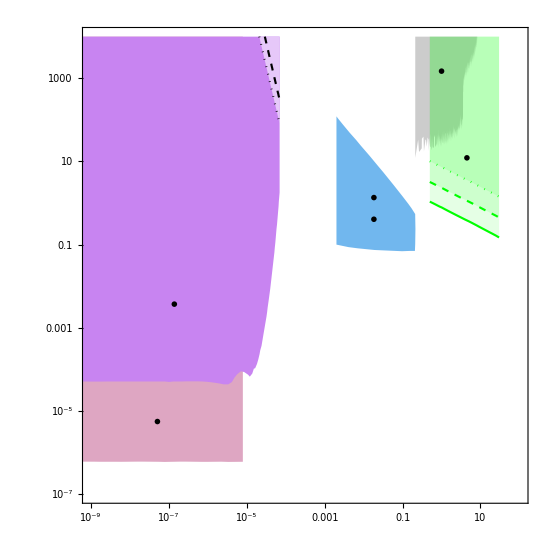

```mathematica
p1ee=Show[ListLogLogPlot[{Reverse[Beamdump],Beamdump,RedGiant,edelweiss(*, Belle4tab,A3tab*),0*Borexino,Babarplot,EWlifetime14,EWlifetime1,CMSCah0p01,CMSCah0p1,CMSCah1},Joined->True,Frame->True,Axes->False,FrameTicksStyle->Black,FrameTicks->{{{{10^4,""},{10^3,"10^3"},{10^2,""},{10,""},{1,"1"},{0.1,""},{10^-2,""},{10^-3,"10^-3"},{10^-4,""},{10^-5,""},{10^-6,"10^-6"},{10^-7,""},{10^-8,""},{10^-9,"10^-9"}},{{10^4,""},{10^3,""},{10^2,""},{10,""},{1,""},{0.1,""},{10^-2,""},{10^-3,""},{10^-4,""},{10^-5,""},{10^-6,""},{10^-7,""},{10^-8,""},{10^-9,""}}},{{{10^3,"10^3"},{10^2,""},{10,""},{1,"1"},{10^-1,""},{10^-2,""},{10^-3,"10^-3"},{10^-4,""},{10^-5,""},{10^-6,"10^-6"},{10^-7,""},{10^-8,""},{10^-9,"10^-9"}},{{10^3,""},{10^2,""},{10,""},{1,""},{10^-1,""},{10^-2,""},{10^-3,""},{10^-4,""},{10^-5,""},{10^-6,""},{10^-7,""},{10^-8,""},{10^-9,""}}}},PlotStyle->{None,None,None,None,None,None,{Dashed,Black,Thickness[0.0028]},{Dotted,Black,Thickness[0.0028]},{Dotted,Green,Thickness[0.0028]},{Dashed,Green,Thickness[0.0028]},{Green,Thickness[0.0028]},None,None,None,Thickness[0.002],Thickness[0.002],Thickness[0.004],Thickness[0.004]},FrameStyle->Thickness[0.003],PlotRange->{{10^-9,10^2},{10^-7,10^4}},
Filling->{1->{{2},colors[[4]]},3->{Top,colors[[6]]},4->{Top,colors[[3]]},5->{Top,colors[[5]]},6->{Top,Directive[Gray,Opacity[.4]]},7->{Top,Lighter[Lighter[colors[[3]]]]},8->{Top,Lighter[Lighter[colors[[3]]]]},9->{Top,Directive[Green,Opacity[.1]]},10->{Top,Directive[Green,Opacity[.1]]},11->{Top,Directive[Green,Opacity[.1]]} }
],
Graphics[{
(*Text[MaTeX["\\text{Borexino}",Magnification->1.5],{-7.5,-3},Automatic]*)Text[MaTeX["\\text{Edelweiss}",Magnification->1.6],{-15.8,-5.6},Automatic],
Text[MaTeX["\\text{Red Giants}",Magnification->1.6],{-16.8,-12.1},Automatic],Text[MaTeX["\\text{BaBar}",Magnification->1.6],{0.,7.3},Automatic,{1,0}],
Text[MaTeX["\\text{Beam}",Magnification->1.3],{-4,5.3-5},Automatic,{1,-.6}],Text[MaTeX["\\text{Dump}",Magnification->1.3],{-4,4.1-5},Automatic,{1,-.6}],
Text[MaTeX["\\textbf{\color{green}CMS}",Magnification->1.6],{1.5,2.5},Automatic],(*Text[MaTeX[" Z \\rightarrow a \\gamma",Magnification->1.6],{7.,-1.5},Automatic,{1.8,-2.}]*)(*Text[MaTeX[" \\text{BaBar}",Magnification->1.2],{1.1,7},Automatic,{1,0.}],Text[MaTeX[" \\text{A1}",Magnification->1.3],{-2,7.3},Automatic,{1,0.}]*)
}],

(*AspectRatio->1,FrameLabel->{MaTeX[" m_a \\, [\\text{GeV}] ",Magnification->2.],MaTeX[" |c_{\\ell\\ell}^\\text{eff}\\Lambda \\, [\\text{TeV}^{-1}]",Magnification->2.],AspectRatio->1,*)
FrameLabel->{MaTeX[" m_a \\, [\\text{GeV}] ",Magnification->2.],MaTeX[" |c_{\\ell\\ell}^{eff}|/\\Lambda \\, [\\text{TeV}^{-1}]",Magnification->2.],None,Style["",Bold]},ImageSize->550,AspectRatio->1,MyOptions]
```

```mathematica
FixPolygons[%]
```

-Graphics-